# Linear Discriminant Analysis (LDA)

### Carlos Manuel Rodríguez Martínez 23/08/2020

## Base de datos Iris, Proyección D’ = 2

Cargar base de datos Iris

Carga toda la base de datos Iris

```mathematica
{{rawAttributes},database} = TakeDrop[Import[FileNameJoin[{NotebookDirectory[],"iris.csv"}]],1];
```

```mathematica
attributes = Drop[rawAttributes,-1]
```

{sepal-length,sepal-width,petal-length,petal-width}

Cambia las etiquetas setosa a 1, y versicolor a 0.

```mathematica
classes = DeleteDuplicates[rawDatabase[[All,-1]]]
```

{setosa,versicolor,virginica}

Se muestrea aleatoriamente la base de datos, tomando el 80% de las muestras para el conjunto de entrenamiento, y el 20% restante para el conjunto de validación.

```mathematica
{trainingSet,validationSet} = TakeDrop[RandomSample[database],Floor[0.8*Length[database]]];
```

### Funciones auxiliares para acceder a la base de datos a través de etiquetas

```mathematica
SelectClass[data_,class_]:=Cases[data,{__,class}][[All,1;;-2]];
ClassSampleSize[data_,class_]:=Length[SelectClass[data,class]];
ClassPercentage[data_,class_]:=ClassSampleSize[data,class]/Length[data];
SelectAttribute[data_,attribute_]:=Block[{positionIndex,datasetByAttribute},
positionIndex = First@FirstPosition[attributes,attribute];
datasetByAttribute = data[[All,{positionIndex,-1}]]
];
SelectAttributes[data_]:=data[[All,1;;-2]];
SelectAttributeInClass[data_,attribute_,class_]:=Flatten@SelectClass[SelectAttribute[data,attribute],class];
```

Ejemplo: Seleccionar el atributo petal-length de la clase setosa.

```mathematica
SelectAttributeInClass[trainingSet,"petal-length","setosa"]
```

{1.4,1.6,1.3,1.6,1.4,1.4,1.7,1.2,1.5,1.5,1.6,1.7,1.4,1.4,1.3,1.5,1.9,1.5,1.7,1.3,1.3,1.5,1.3,1.5,1.5,1.9,1.6,1.6,1.7,1.4,1.5,1.4,1.5,1.1,1.4,1.,1.3,1.4}

### Visualización de la distribución de los atributos

Se separan los atributos por clase

```mathematica
sepalLengthByClass = Map[SelectAttributeInClass[trainingSet,"sepal-length",#]&,classes];
sepalWidthByClass = Map[SelectAttributeInClass[trainingSet,"sepal-width",#]&,classes];
petalLengthByClass = Map[SelectAttributeInClass[trainingSet,"petal-length",#]&,classes];
petalWidthByClass = Map[SelectAttributeInClass[trainingSet,"petal-width",#]&,classes];
```

Distribuciones de los atributos por clase:

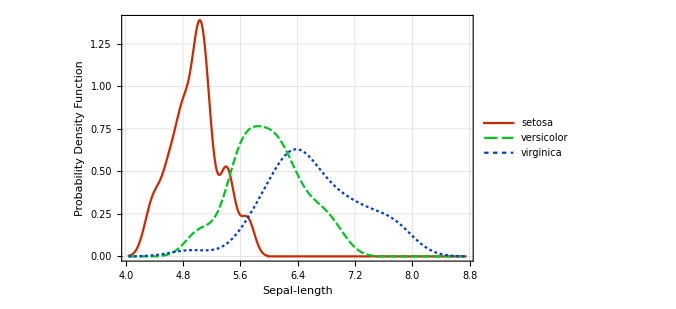

```mathematica
SmoothHistogram[
sepalLengthByClass,
PlotLegends->classes,
PlotTheme->"Monochrome",
FrameLabel->{Style["Sepal-length",15], Style["Probability Density Function",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.76, 0.13],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500,
PlotRange->All
]
```

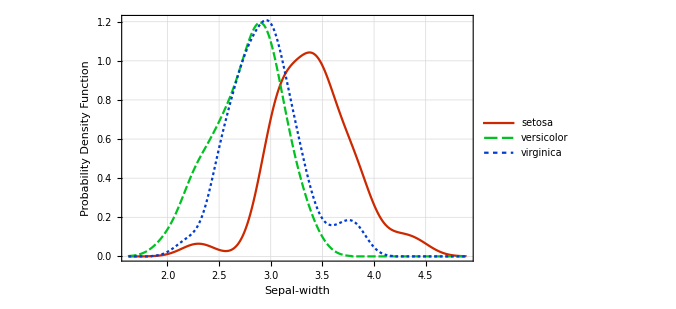

```mathematica
SmoothHistogram[
sepalWidthByClass,
PlotLegends->classes,
PlotTheme->"Monochrome",
FrameLabel->{Style["Sepal-width",15], Style["Probability Density Function",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.76, 0.13],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500,
PlotRange->All
]
```

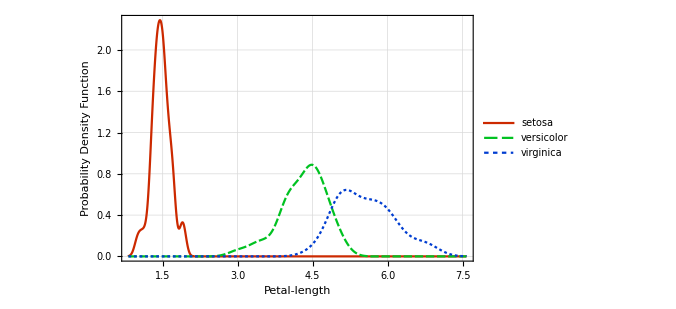

```mathematica
SmoothHistogram[
petalLengthByClass,
PlotLegends->classes,
PlotTheme->"Monochrome",
FrameLabel->{Style["Petal-length",15], Style["Probability Density Function",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.76, 0.13],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500,
PlotRange->All
]
```

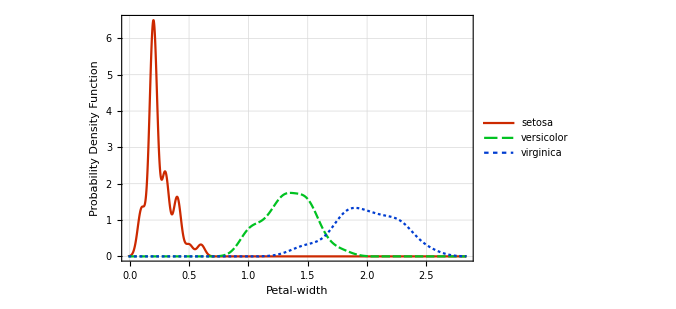

```mathematica
SmoothHistogram[
petalWidthByClass,
PlotLegends->classes,
PlotTheme->"Monochrome",
FrameLabel->{Style["Petal-width",15], Style["Probability Density Function",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.76, 0.13],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500,
PlotRange->All
]
```

Implementación de Linear Discriminant Analysis (LDA)

### Vector promedio por clase

```mathematica
ClassMeanVector[data_,class_]:=Map[Mean[SelectAttributeInClass[data,#,class]]&,attributes];
```

#### Ejemplos:

Vector promedio con toda la base de datos

```mathematica
meanVectors = Map[ClassMeanVector[database,#]&,classes]
```

{{5.006,3.418,1.464,0.244},{5.936,2.77,4.26,1.326},{6.588,2.974,5.552,2.026}}

Vector promedio para el conjunto de entrenamiento

```mathematica
meanVectors = Map[ClassMeanVector[trainingSet,#]&,classes]
```

{{4.97632,3.40526,1.46842,0.252632},{5.97857,2.77143,4.30714,1.3381},{6.62,2.95,5.5625,1.995}}

### Within-Class scatter matrix S_w

```mathematica
WithinClassScatterMatrixSi[data_,class_]:=Block[{classMeanVector,classAttributes,semiSi},
classMeanVector =ClassMeanVector[data,class];
classAttributes = SelectClass[data,class];
semiSi = Map[#-classMeanVector&,classAttributes];
Transpose[semiSi].semiSi
];
WithinClassScatterMatrixSW[data_]:=Total[Map[WithinClassScatterMatrixSi[data,#]&,classes]];
```

#### Ejemplos:

S_i para la clase setosa

```mathematica
WithinClassScatterMatrixSi[database,"setosa"]
```

{{6.0882,4.9146,0.7908,0.5168},{4.9146,7.1138,0.5724,0.5604},{0.7908,0.5724,1.4752,0.2792},{0.5168,0.5604,0.2792,0.5632}}

S_w con toda la base de datos

```mathematica
WithinClassScatterMatrixSW[database]
```

{{38.9562,13.683,24.614,5.6556},{13.683,17.035,8.12,4.9132},{24.614,8.12,27.22,6.2536},{5.6556,4.9132,6.2536,6.1756}}

S_w con el conjunto de entrenamiento

```mathematica
WithinClassScatterMatrixSW[trainingSet]
```

{{30.8034,11.339,19.888,5.04565},{11.339,14.4647,7.18989,4.34519},{19.888,7.18989,22.6237,5.40423},{5.04565,4.34519,5.40423,4.89278}}

### Between-class scatter matrix S_B

```mathematica
CalculateOverallMean[data_]:=Mean[Flatten[Map[SelectClass[data,#]&,classes],1]];
BetweenClassScatterMatrixSB[data_]:=Block[{overallMean,semiSbi},
overallMean = CalculateOverallMean[data];
semiSbi = Map[√ClassSampleSize[data,#]*(ClassMeanVector[data,#]-overallMean)&,classes];

Transpose[semiSbi].semiSbi
];
```

#### Ejemplos:

S_B con toda la base de datos

```mathematica
BetweenClassScatterMatrixSB[database]
```

{{63.2121,-19.534,165.165,71.3631},{-19.534,10.9776,-56.0552,-22.4924},{165.165,-56.0552,436.644,186.908},{71.3631,-22.4924,186.908,80.6041}}

S_B con el conjunto de entrenamiento

```mathematica
BetweenClassScatterMatrixSB[trainingSet]
```

{{53.3416,-16.324,134.352,56.6443},{-16.324,8.41501,-44.4012,-17.5559},{134.352,-44.4012,341.551,142.883},{56.6443,-17.5559,142.883,60.1659}}

### Descomposición por eigenvalores

Cómputo de la matriz S_w

```mathematica
Sw = WithinClassScatterMatrixSW[trainingSet];
MatrixForm[Sw]
```

(30.8034 | 11.339 | 19.888 | 5.04565
11.339 | 14.4647 | 7.18989 | 4.34519
19.888 | 7.18989 | 22.6237 | 5.40423
5.04565 | 4.34519 | 5.40423 | 4.89278)

Cómputo de la matriz S_B

```mathematica
Sb = BetweenClassScatterMatrixSB[trainingSet];
MatrixForm[Sb]
```

(53.3416 | -16.324 | 134.352 | 56.6443
-16.324 | 8.41501 | -44.4012 | -17.5559
134.352 | -44.4012 | 341.551 | 142.883
56.6443 | -17.5559 | 142.883 | 60.1659)

Cálculo de los eigenvalores y eigenvectores ordenados de mayor a menor según la magnitud del eigenvalor

```mathematica
{eigenValues, eigenVectors} = Eigensystem[Inverse[Sw].Sb]
```

{{30.9417,0.227966,6.70996×10^-15,1.80175×10^-15},{{0.181165,0.407835,-0.49617,-0.744759},{-0.00552148,-0.555709,0.25876,-0.790063},{-0.382526,-0.172399,-0.238349,0.875867},{-0.794707,0.115688,0.0806669,0.59038}}}

```mathematica
sorted = Reverse[SortBy[Transpose[{eigenValues, eigenVectors}],First]]
```

{{30.9417,{0.181165,0.407835,-0.49617,-0.744759}},{0.227966,{-0.00552148,-0.555709,0.25876,-0.790063}},{6.70996×10^-15,{-0.382526,-0.172399,-0.238349,0.875867}},{1.80175×10^-15,{-0.794707,0.115688,0.0806669,0.59038}}}

Varianza explicada por eigenvalor

```mathematica
Re[100*eigenValues/Total[eigenValues]]
```

{99.2686,0.731373,2.15272×10^-14,5.78045×10^-15}

Implementación en una función:

```mathematica
CalculateEigenvectorMatrixW[data_,dimensions_]:=Block[{Sw,Sb,eigenValues, eigenVectors,sorted},
Sw = WithinClassScatterMatrixSW[data];
Sb = BetweenClassScatterMatrixSB[data];
{eigenValues, eigenVectors} = Eigensystem[Inverse[Sw].Sb];
sorted = Reverse[SortBy[Transpose[{eigenValues, eigenVectors}],First]];
Re[Transpose[Take[sorted[[All,2]],dimensions]]]
];
ProjectClass[data_,class_,W_]:=SelectClass[data,class].W;
ProjectData[data_,W_]:=data.W;
```

```mathematica
W = CalculateEigenvectorMatrixW[trainingSet,2]
```

{{0.181165,-0.00552148},{0.407835,-0.555709},{-0.49617,0.25876},{-0.744759,-0.790063}}

```mathematica
MatrixForm[W]
```

(0.181165 | -0.00552148
0.407835 | -0.555709
-0.49617 | 0.25876
-0.744759 | -0.790063)

#### Visualización de la proyección

```mathematica
setosaProyection = ProjectClass[trainingSet,"setosa",W];
versicolorProyection = ProjectClass[trainingSet,"versicolor",W];
virginicaProyection = ProjectClass[trainingSet,"virginica",W];
```

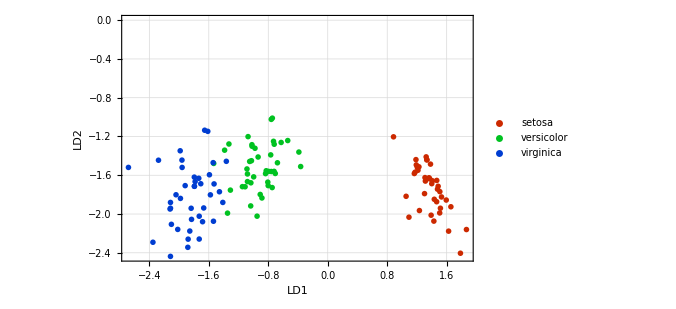

```mathematica
ListPlot[
{setosaProyection,versicolorProyection,virginicaProyection},
PlotLegends->classes,
PlotTheme->"Monochrome",
FrameLabel->{Style["LD1",15], Style["LD2",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.76, 0.13],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500,
PlotRange->All
]
```

### Clasificación por medio de maximización de probabilidad posterior en distribución gaussiana multinomial

```mathematica
FitMultivariateGaussian[proyectedData_]:=Block[{distributionParameters,μ1,μ2,σ1,σ2,ρ,ld1,ld2},
distributionParameters = FindDistributionParameters[proyectedData,BinormalDistribution[{μ1,μ2},{σ1,σ2},ρ]];
PDF[BinormalDistribution[{μ1,μ2},{σ1,σ2},ρ]/.distributionParameters,{ld1,ld2}]
];
```

Distribuciones de los puntos proyectados por clase

```mathematica
setosaGaussian = FitMultivariateGaussian[setosaProyection]
```

4.40429 ⅇ^(-0.891629 (26.7887 (-1.37358+ld1)^2+27.4678 (-1.37358+ld1) (1.73944+ld2)+16.0304 (1.73944+ld2)^2))

```mathematica
versicolorGaussian = FitMultivariateGaussian[versicolorProyection]
```

2.81756 ⅇ^(-0.533004 (16.079 (0.92024+ld1)^2-8.53341 (0.92024+ld1) (1.51578+ld2)+18.2846 (1.51578+ld2)^2))

```mathematica
virginicaGaussian = FitMultivariateGaussian[virginicaProyection]
```

1.92454 ⅇ^(-0.516767 (14.0207 (1.84331+ld1)^2-4.28508 (1.84331+ld1) (1.81272+ld2)+10.0907 (1.81272+ld2)^2))

### Visualización de la proyección del conjunto de entrenamiento y las distribuciones multinomiales ajustadas

Funciones auxiliares para la gráfica:

```mathematica
TransparentGradient[z_, gradient_ : "BlueGreenYellow"]:=RGBColor[Append[Apply[List,ColorData[gradient][z]],z]];
BoundingBox[data_,offset_ : 0.1]:={
Min[data[[All,1]]]-offset,
Max[data[[All,1]]]+offset,
Min[data[[All,2]]]-offset,
Max[data[[All,2]]]+offset
};
```

Visualización de proyección y distribución:

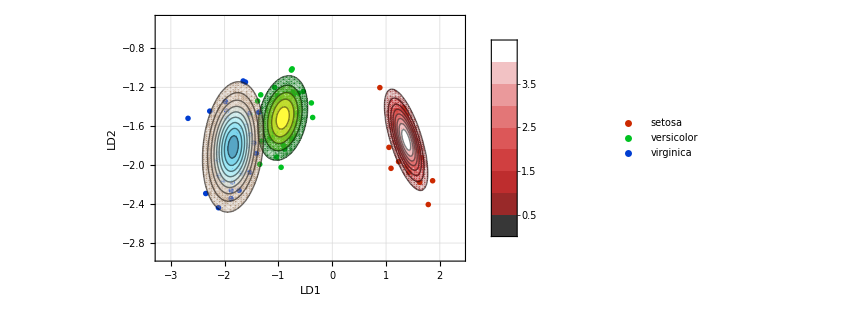

```mathematica
{xMin,xMax,yMin,yMax} = BoundingBox[Join[setosaProyection,versicolorProyection,virginicaProyection],0.5];
Show[
ListPlot[
{setosaProyection,versicolorProyection,virginicaProyection},
PlotRange->{{xMin,xMax},{yMin,yMax}},
PlotLegends->classes,
PlotTheme->"Monochrome",
FrameLabel->{Style["LD1",15], Style["LD2",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.76, 0.13],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500
],
ContourPlot[setosaGaussian,{ld1,xMin,xMax},{ld2,yMin,yMax},PlotRange->All,ColorFunction->(TransparentGradient[#,"CherryTones"]&),PlotLegends->Automatic],
ContourPlot[versicolorGaussian,{ld1,xMin,xMax},{ld2,yMin,yMax},PlotRange->All,ColorFunction->(TransparentGradient[#,"AvocadoColors"]&),PlotLegends->Automatic],
ContourPlot[virginicaGaussian,{ld1,xMin,xMax},{ld2,yMin,yMax},PlotRange->All,ColorFunction->(TransparentGradient[#,"BrownCyanTones"]&),PlotLegends->Automatic]
]
```

Clasificación sobre el conjunto de validación

### Visualización de la proyección del conjunto de validación y las distribuciones ajustadas al conjunto de entrenamiento

```mathematica
setosaProyectionValidation = ProjectClass[validationSet,"setosa",W];
versicolorProyectionValidation = ProjectClass[validationSet,"versicolor",W];
virginicaProyectionValidation = ProjectClass[validationSet,"virginica",W];
```

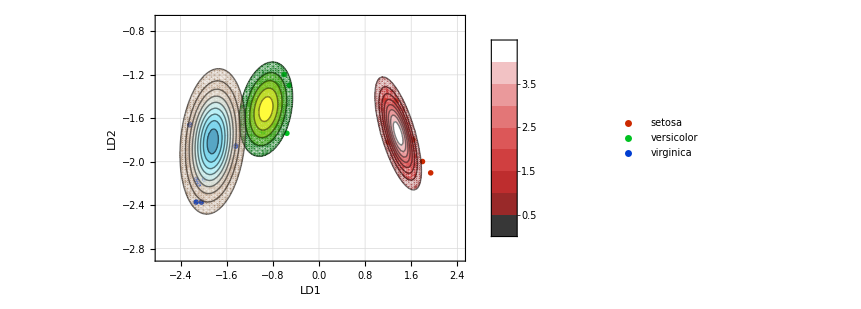

```mathematica
{xMin,xMax,yMin,yMax} = BoundingBox[Join[setosaProyectionValidation,versicolorProyectionValidation,virginicaProyectionValidation],0.5];
Show[
ListPlot[
{setosaProyectionValidation,versicolorProyectionValidation,virginicaProyectionValidation},
PlotRange->{{xMin,xMax},{yMin,yMax}},
PlotLegends->classes,
PlotTheme->"Monochrome",
FrameLabel->{Style["LD1",15], Style["LD2",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.76, 0.13],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500
],
ContourPlot[setosaGaussian,{ld1,xMin,xMax},{ld2,yMin,yMax},PlotRange->All,ColorFunction->(TransparentGradient[#,"CherryTones"]&),PlotLegends->Automatic],
ContourPlot[versicolorGaussian,{ld1,xMin,xMax},{ld2,yMin,yMax},PlotRange->All,ColorFunction->(TransparentGradient[#,"AvocadoColors"]&),PlotLegends->Automatic],
ContourPlot[virginicaGaussian,{ld1,xMin,xMax},{ld2,yMin,yMax},PlotRange->All,ColorFunction->(TransparentGradient[#,"BrownCyanTones"]&),PlotLegends->Automatic]
]
```

### Clasificación por medio de la maximización de la probabilidad posterior

```mathematica
CalculateGaussianPDFValue[{x1_,x2_},dist_]:=ReplaceAll[dist,{ld1->x1, ld2-> x2}];
CalculateProbabilityOfClass[point_,class_]:=Block[{distribution},
distribution = ReplaceAll[class,{"setosa"->setosaGaussian,"versicolor"->versicolorGaussian,"virginica"->virginicaGaussian}];

CalculateGaussianPDFValue[point,distribution]*ClassPercentage[trainingSet,class]
];
ClassifyProjectedPoint[point_]:=Block[{probabilities},
probabilities = Table[
{CalculateProbabilityOfClass[point,class],class},
{class,classes}
];
MaximalBy[probabilities,First][[1,2]]
];
```

#### Ejemplo:

Utilizando el primer punto de la proyección del conjunto de validación para la clase setosa

```mathematica
dataPoint = First[setosaProyectionValidation]
```

{1.26762,-1.48993}

se calculan las probabilidades posteriores:

```mathematica
Column@Table[
Row[{"P("<>class<>"| x = "<>ToString[dataPoint]<>") = ",CalculateProbabilityOfClass[dataPoint,class]}],
{class,classes}
]
```

P(setosa| x = {1.26762, -1.48993}) = 0.837093
P(versicolor| x = {1.26762, -1.48993}) = 1.9351×10^-18
P(virginica| x = {1.26762, -1.48993}) = 1.2132×10^-30

La probabilidad es máxima para la clase setosa.

#### Clasificación para todo el conjunto de validación

Puntos proyectados:

```mathematica
proyectedValidationSet = ProjectData[SelectAttributes[validationSet],W]
```

{{1.26762,-1.48993},{-0.936422,-1.47163},{-1.986,-2.15858},{1.93774,-2.10236},{-1.66842,-1.70195},{1.53089,-1.88385},{-2.12519,-2.16449},{1.32277,-1.84711},{1.41737,-1.68744},{1.62986,-1.79697},{-0.764455,-1.66421},{-1.76429,-1.89911},{-0.515607,-1.29691},{-0.872158,-1.48478},{-0.605376,-1.19672},{-0.557153,-1.73802},{-1.64576,-1.75697},{1.13626,-1.4316},{1.33327,-1.44062},{-0.934513,-1.62605},{1.29484,-1.59942},{-2.03799,-2.37129},{1.57596,-1.85526},{1.79545,-1.99799},{-1.44319,-1.855},{-0.971043,-1.72862},{-2.23836,-1.66041},{-2.1304,-2.37106},{-2.08788,-2.20679},{1.20069,-1.81903}}

Clases obtenidas por medio del algoritmo de clasificación:

```mathematica
classificationsOfValidation = Map[ClassifyProjectedPoint,proyectedValidationSet]
```

{setosa,versicolor,virginica,setosa,virginica,setosa,virginica,setosa,setosa,setosa,versicolor,virginica,versicolor,versicolor,versicolor,versicolor,virginica,setosa,setosa,versicolor,setosa,virginica,setosa,setosa,virginica,versicolor,virginica,virginica,virginica,setosa}

Clases del conjunto de validación:

```mathematica
classesOfValidation = validationSet[[All,-1]]
```

{setosa,versicolor,virginica,setosa,virginica,setosa,virginica,setosa,setosa,setosa,versicolor,virginica,versicolor,versicolor,versicolor,versicolor,virginica,setosa,setosa,versicolor,setosa,virginica,setosa,setosa,virginica,versicolor,virginica,virginica,virginica,setosa}

Comparación entre clases del conjunto de validación y las obtenidas por medio de la clasificación:

```mathematica
classVsClassification = Transpose[{classesOfValidation,classificationsOfValidation}];
Grid[
Prepend[classVsClassification,{"Clase","Clasificación"}],
Frame->All,
Background->{None,{LightGreen}}
]
```

Clase | Clasificación
setosa | setosa
versicolor | versicolor
virginica | virginica
setosa | setosa
virginica | virginica
setosa | setosa
virginica | virginica
setosa | setosa
setosa | setosa
setosa | setosa
versicolor | versicolor
virginica | virginica
versicolor | versicolor
versicolor | versicolor
versicolor | versicolor
versicolor | versicolor
virginica | virginica
setosa | setosa
setosa | setosa
versicolor | versicolor
setosa | setosa
virginica | virginica
setosa | setosa
setosa | setosa
virginica | virginica
versicolor | versicolor
virginica | virginica
virginica | virginica
virginica | virginica
setosa | setosa

La tasa de clasificación es del 100 %

```mathematica
100*Count[classVsClassification,{x_,y_}/;x==y]/Length[validationSet]
```

100